Deutsch-Jozsa Algorithm

Statement of  the Problempaclet:Q3/tutorial/DeutschJozsaAlgorithm#3657172 | Examplespaclet:Q3/tutorial/DeutschJozsaAlgorithm#1201453173
Quantum Implementationpaclet:Q3/tutorial/DeutschJozsaAlgorithm#1347293990 |

See also Section 4.2 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

Proposed first by Deutsch & Jozsa (1992), the algorithm determines whether a given function is balanced or constant. It is of little use in practice, but it is one of the first examples of a quantum algorithm that is exponentially faster than any possible classical algorithms. Furthermore, it is so simple that it clearly reveals some aspects of quantum parallelism and the operational principle of the quantum oracle.

Oraclepaclet:Q3/ref/OracleQ3 Package Symbol | Represents a quantum implementation of classical oracle.
ControlledPowerpaclet:Q3/ref/ControlledPowerQ3 Package Symbol | Controlled exponentiation of a unitary gate

Q3 functions used in the Deutsch-Jozsa algorithm.

Make sure that the Q3 package is loaded to use the demonstrations in this document.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Statement of  the Problem

Consider a classical function f:{0, 1}^n→{0, 1}. It is a classical oracle taking n-bit inputs and returning 0 or 1. The function is promised to be either constant (either 0 or 1 for all inputs) or balanced (0 for one half of the possible inputs and 1 for the other half). The task is to determine whether f is constant or balanced by using the oracle the least number of times.

In classical algorithms, one has to evaluate the oracle (2^(n-1)+1)≈2^n/2 times in the worst case. That is, one has to try almost half of the possible inputs before reliably determining the unknown property of the oracle. As we will see now, the Deutsch-Jozsa algorithm determines the property from a single query to the quantum oracle.

Quantum Implementation

The quantum circuit in Figure 1 summarizes the Deutsch-Jozsa algorithm. The last qubit is an ancillary qubit that induces the conditional phase shifts on the first n qubits. The Hadamard gate on it ensures that the ancillary qubit is in the eigenstate -:=(0-1)/(√2) of the Pauli X operator just before the quantum oracle operates.

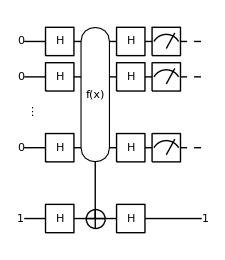

Figure 1. A quantum circuit for the Deutsch-Jozsa algorithm.

The Hadamard gates on the native register before the quantum oracle create a linear superposition of all the logical basis states of the n-qubit native register (normalization ignored)

0↦1/2^(n/2)Σ_(x=0)^(2^n-1)x.

Next, the quantum oracle induces the conditional phase shifts

1/2^(n/2)Σ_(x=0)^(2^n-1)x↦1/2^(n/2)Σ_(x=0)^(2^n-1)(x(-1))^(f(x)) .

Another operation of the Hadamard gates shuffles and causes additional phase factors specific to the Hadamard gate, and it leads to the output state to be measured

1/2^(n/2)Σ_(x=0)^(2^n-1)(x(-1))^(f(x))↦1/2^n Σ_(y=0)^(2^n-1)y(Σ_(x=0)^(2^n-1)(-1))^(f(x)+x·y).

To see the effect of the function f on the final state, suppose that f is a constant function. Then, the output state is given by

(-1)^(f(0))/2^n Σ_(y=0)^(2^n-1)y(Σ_(x=0)^(2^n-1)(-1))^(x·y)=(-1)^(f(0))0.

Every measurement on each of the n qubits should yield zero with unit probability.

To make the analysis more explicit, consider the probability to find the n-qubit register in the state 0≡0⊗0⊗⋯⊗0

P_0=1/2^n(|(Σ_(x=0)^(2^n-1)(-1))^(f(x))|)^2.

This assures that P_0=1 for a constant function f. When the function f is balanced, there are as many terms with −1 as 1, and the sum is always zero. There must be at least one qubit in the state 1 if the function f is balanced. Therefore, to determine whether a given function f is constant or balanced, one needs to run the quantum oracle just once, and then check whether the measurement outcome is 0. If the outcome is 0, then the function must be constant; and balanced otherwise.

Examples

### Constant Function

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S,T]
Let[Complex,c]
```

Consider a balanced function as an example.

```mathematica
Clear[f];
f[{0,0}]=f[{1,1}]=1;
f[{0,1}]=f[{1,0}]=1;
```

Here is a quantum circuit for the Deutsch-Jozsa algorithm. The final Hadamard gate on the third qubit is not necessary, but we put it here to make the output state more readable.

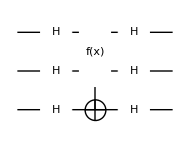

```mathematica
SS=S[{1,2},$];
TT=T@{$};
all=Join[SS,TT];
qc=QuantumCircuit[Ket[SS],Ket[TT->1],
Through[all[6]],Oracle[f,SS,TT],Through[all[6]]
]
```

```mathematica
out=Elaborate[qc];
ProductForm[out,{SS,TT}]
```

-⊗⊗001

### Balanced Function

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S,T]
Let[Complex,c]
```

Consider a balanced function as an example.

```mathematica
Clear[f];
f[{0,0}]=f[{1,0}]=0;
f[{0,1}]=f[{1,1}]=1;
```

Here is a quantum circuit for the Deutsch-Jozsa algorithm. The final Hadamard gate on the third qubit is not necessary, but we put it here to make the output state more readable.

```mathematica
SS=S[{1,2},$];
TT=T@{$};
all=Join[SS,TT];
qc=QuantumCircuit[Ket[SS],Ket[TT->1],
Through[all[6]],Oracle[f,SS,TT],Through[all[6]]
]
```

-Graphics-

```mathematica
out=Elaborate[qc];
ProductForm[out,{SS,TT}]
```

⊗⊗011

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Decision Algorithms
▪Quantum Algorithms
▪Quantum Information Systems with Q3

| Related Links
▪D. Deutsch and R. Jozsa, Proceedings of the Royal Society A: Mathematical, Physical and Engineering Sciences 439 (1907), 553 (1992)https://doi.org/10.1098/rspa.1992.0167, “Rapid Solution of Problems by Quantum Computation.”
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).